# Numerical Lab 5: Fourier Transform

For all problems on this assignment, remember to typeset special characters as well as superscripts and subscripts.

## Discrete Fourier Transform Problems

Functions Used: Riemann integral from Numerical Lab 3

Find our implementation of the Riemann integral from Numerical Lab 3, and copy it into this notebook. Evaluate it so that it’s stored in memory.

Use the Riemann integration function your write for Lab 3 to create a function DFT whose inputs are the function p, the desired number of time steps n, the period T, and the integer j, and whose output is the coefficient a_j. Notice that the time step will be Δt = T/n.

Check your DFT function on the function Sin[4π t/T] for the value T = 1s. Notice that this sine wave has frequency 2 Hz. Does the result match your expectation?

## Your Solutions

1.

```mathematica
RiemannSum[f_,left_,right_,Δx_]:=Δx Sum[f[left+k Δx],{k,0,Floor[(right-left)/Δx]-1}]//N
```

2.

```mathematica
a=DFT[p_,n_,T_,j_]:=1/T RiemannSum[p[#] ⅇ^(-2π ⅈ(j#/T))&,0,T,T/n]//N
```

3.

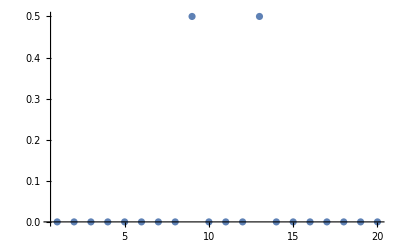

```mathematica
ListPlot[Abs/@Table[DFT[Sin[4π#]&,20,1,j],{j,-10,9}],PlotRange->All]
```

The result matches the expectation.

## Inverse Discrete Fourier Transform Problems

Functions Used: “Sum”, “ListPlot”, “Re” (real part function), “Im” (imaginary part function).

Write a function whose inputs are the list of values a = {a_(-n/2),a_(-n/2+1),…,a_(n/2-1)}, the period T, and the time parameter k (such that t = k T/n), and whose output is p(t).

Try plugging a list a into your function that has only one non-zero element. What type of function do you expect, and what type do you get? You can check this out using the “ListPlot” function on your output.

## Your Solutions

1.

```mathematica
IDFT[a_,T_,k_]:=Sum[a[[j]] ⅇ^(2π ⅈ k((j-(Length[a]/2-1))/Length[a])),{j,1,Length[a]}]//N
```

2.

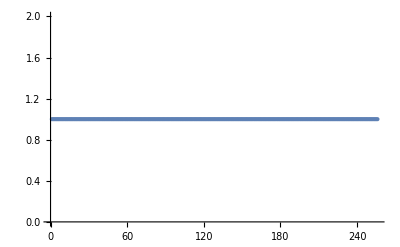

```mathematica
ListPlot[Abs[Table[IDFT[{0,0,1,0,0},1,i],{i,-127,128}]],PlotRange->All]
```

## Book Problems

MMOW 8.6.3

MMOW 8.6.4

## Your Solutions

1.

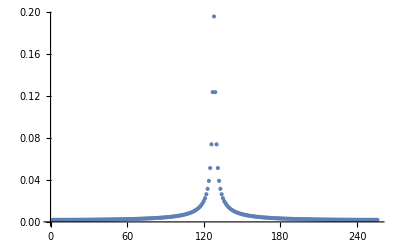

```mathematica
ListPlot[Abs[Table[DFT[ⅇ^-#&,256,256/50,i],{i,-127,128}]],PlotRange->All]
```

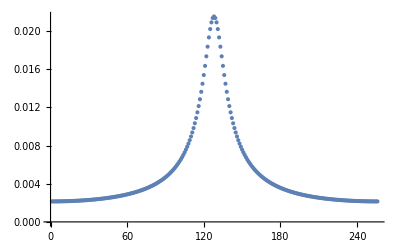

```mathematica
ListPlot[Abs[Table[DFT[ⅇ^(-10#)&,256,256/50,i],{i,-127,128}]],PlotRange->All]
```

The power spectrum is shifted upward and gets wider, or less sharply peaked.

2.

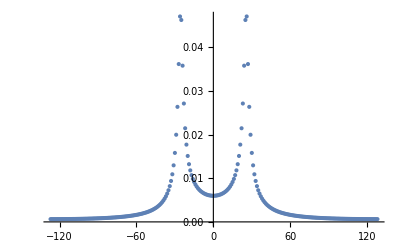

```mathematica
ListPlot[Transpose[
{Table[i,{i,-127,128}],Abs[Table[DFT[ⅇ^(-2#)Sin[2π 5#]&,256,256/50,i],{i,-127,128}]]}],PlotRange->All]
```

The peak was shifted to the right.

## Applied Problems

I will provide you with an audio file (a function of amplitude over time) of time length T and time spacing Δt. Use your DFT algorithm to decompose the file into its frequency components. Use “ListPlot” to plot a_j for this function for j = -n/2 to j = n/2.

Take the values a_j you found in the last problem and create a new list of values b_j composed of all the a_j elements {a_(-n/4),a_(-n/4+1),…,a_(n/4-2),a_(n/4-1)} (in other words, delete all the high frequencies).

Take the IDFT of the list of b_j values you just constructed. Use “ListPlot” to compare the IDFT of this list to the list of amplitudes of the original function at each time step. How different do they seem?

```mathematica
NormalizedListDifference[list1_,list2_]:=Module[{tuplelist},
tuplelist=Transpose[{list1,list2}];
Total[Abs[#[[1]]-#[[2]]]&/@tuplelist]/Mean[list1]
]
```

The function above provides a measure of how different list2 is from list1. Use this function to check how different the original list of amplitudes is from the IDFT of the list b_j.

## Your Solutions

1.

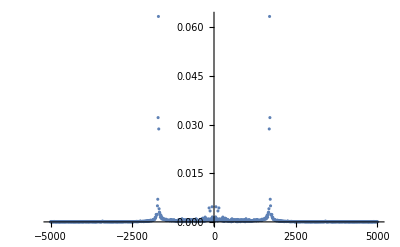

```mathematica
aj=Table[{10j,Abs[DFT[tuesf ,1000,100,j]]},{j,-500,500}];
ListPlot[Table[{10j,Abs[DFT[tuesf ,1000,100,j]]},{j,-500,500}],PlotRange->All]
```

2.

```mathematica
bj=aj[[250;;750]];
```

3.

```mathematica
IDFT[bj,100,]
```